9.81

30

{{a→-(1. (9.81 k m Cos[0.0174533 alfa]-9.81 m Sin[0.0174533 alfa]))/m}}

-(1. (9.81 k m Cos[0.0174533 alfa]-9.81 m Sin[0.0174533 alfa]))/m

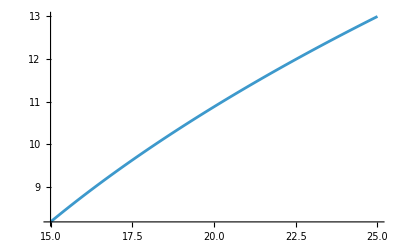

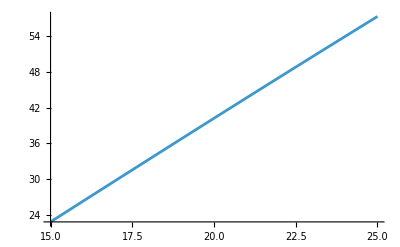

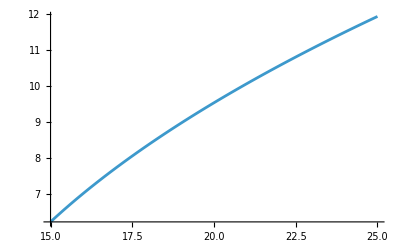

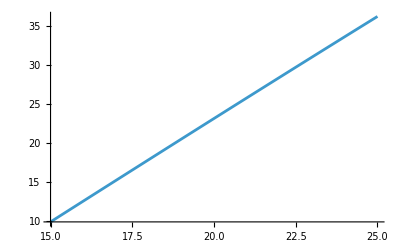

```mathematica
ClearAll["Global`*"]
g=9.81
L=30
rown1=Solve[m*g*Sin[alfa*Degree]-k*m*g*Cos[alfa*Degree]==m*a,a]
A=a/.rown1[[1]]
acc[a_,w_]:=A/.{alfa->a,k->w}
vk[a_,w_]:=Sqrt[2*L*acc[a,w]]
sc[a_,w_]:=(vk[a,w]^2)/(2*w*g)
Plot[vk[a,0.15],{a,15,25}]
Plot[sc[a,0.15],{a,15,25}]
Plot[vk[a,0.2],{a,15,25}]
Plot[sc[a,0.2],{a,15,25}]
```